```mathematica
SetDirectory[NotebookDirectory[]];Get["Packages\\TextbookFigurePreamble.wl"] (* loads libraries, textbook stylings and defines txbExport *)
```

```mathematica
imgFile= "C:\\Users\\jonat\\Documents\\GitHub\\MathematicalPhyllotaxis\\Mathematica\\PreMathematica Figures\\0091_James20.jpg";
(Association@FileInformation[imgFile])["RawByteCount"];
img91 = Import[imgFile];
```

Trim an image by a mask

```mathematica
trimByMask[img_,mask_] := Module[{border,timg,tmask,amask,cmask},
border= BorderDimensions[Binarize@mask];
timg= ImagePad[img,-border];
(* now set nonsalient to white *)
tmask = ImagePad[mask,-border];
amask = SetAlphaChannel[tmask,ColorNegate@tmask];
cmask = ColorNegate@amask;
ImageCompose[timg,cmask]
];
trimBySaliency[img_] := trimByMask[img,ImageSaliencyFilter[img]]
```

```mathematica
t91= trimBySaliency[img91];
```

```mathematica
img= ImageResize[t91,400]
```

-Graphics-

```mathematica
components = ImageSegmentationComponents[img];
```

```mathematica
Colorize[components]
```

-Graphics-

```mathematica
gComponents[img_,components_,seedComponents_:Missing[]]:= Module[{bc,bxy,seeds},
seeds= DeleteDuplicates[Flatten@components];
If[!MissingQ[seedComponents],seeds=seedComponents];
bc = Association@ComponentMeasurements[{img,components},"Contours"];
bc= KeyTake[bc,seeds];
bxy= Association@ComponentMeasurements[{img,components},{"Centroid"}];
bxy=KeyTake[bxy,seeds];
Graphics[{Values[bc],KeyValueMap[Text[#1,First[#2]]&,bxy]}]
];

getNumberedComponentProperties[img_,components_,wantedComponentNumbers_,props_] := KeyTake[Association@ComponentMeasurements[{img,components},props],wantedComponentNumbers
]
```

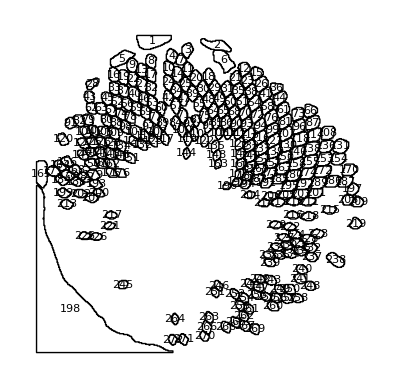

```mathematica
gComponents[img,components]
```

```mathematica
seedComponents= DeleteDuplicates[Flatten@components];
seedComponents= Complement[seedComponents,{1,2,5,6,165,198,238}];
```

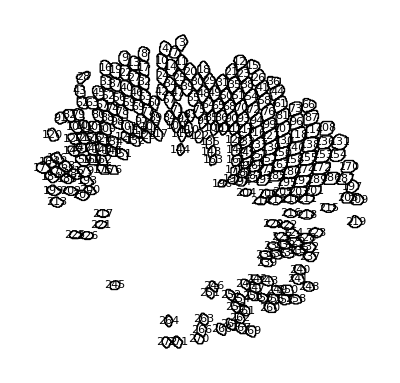

```mathematica
gComponents[img,components,seedComponents]
```

```mathematica
pixelize[xy_]:= Round/@xy;seedCentres = pixelize/@getNumberedComponentProperties[img,components,seedComponents,"Centroid"];
```

```mathematica
head = <|"Tag"->91,"Image"->  ImageResize[t91,400],
"SeedCentres"->seedCentres|>
```

```mathematica
head
```

-Graphics-

```mathematica
seedCentres
```

<|3→{184,369},4→{165,362},7→{176,357},8→{139,356},9→{116,351},10→{161,347},11→{184,346},12→{253,346},13→{128,345},14→{172,340},15→{268,341},16→{94,339},17→{140,339},18→{210,337},19→{106,336},20→{194,335},21→{242,335},22→{117,334},23→{256,332},24→{161,330},25→{181,327},26→{274,328},27→{128,327},28→{68,328},29→{217,323},30→{202,322},31→{232,322},32→{140,322},33→{95,322},34→{170,320},35→{245,319},36→{292,323},37→{106,320},38→{261,318},39→{190,316},40→{119,315},41→{279,315},42→{160,311},43→{64,312},44→{296,311},45→{86,310},46→{130,310},47→{179,309},48→{209,308},49→{223,309},50→{236,306},51→{251,306},52→{98,306},53→{141,305},54→{266,304},55→{198,303},56→{110,303},57→{170,301},58→{281,300},59→{122,298},60→{152,298},61→{300,296},62→{67,298},63→{78,298},64→{215,295},65→{227,294},66→{333,295},67→{91,296},68→{240,293},69→{133,293},70→{254,292},71→{178,289},72→{268,290},73→{318,291},74→{103,291},75→{204,289},76→{286,287},77→{144,287},78→{114,287},79→{63,284},80→{85,283},81→{303,282},82→{52,283},83→{194,283},84→{170,280},85→{219,281},86→{231,281},87→{336,280},88→{97,281},89→{153,280},90→{243,279},91→{42,280},92→{186,278},93→{256,279},94→{272,277},95→{209,276},96→{319,276},97→{137,276},98→{109,275},99→{287,272},100→{177,271},101→{121,269},102→{70,271},103→{147,269},104→{60,270},105→{82,270},106→{223,268},107→{304,267},108→{355,268},109→{95,268},110→{192,266},111→{233,268},112→{246,267},113→{259,266},114→{339,265},115→{132,264},116→{272,262},117→{156,261},118→{321,260},119→{184,261},120→{32,260},121→{289,259},122→{205,259},123→{142,258},124→{118,258},125→{68,257},126→{79,257},127→{57,256},128→{91,255},129→{247,255},130→{305,253},131→{370,252},132→{129,253},133→{259,252},134→{104,252},135→{217,252},136→{353,252},137→{274,249},138→{335,249},139→{289,245},140→{318,244},141→{78,244},142→{66,245},143→{90,243},144→{183,243},145→{248,242},146→{102,241},147→{56,241},148→{220,241},149→{260,239},150→{302,238},151→{114,238},152→{274,236},153→{350,236},154→{367,236},155→{333,233},156→{37,233},157→{287,231},158→{316,230},159→{67,230},160→{79,231},161→{249,230},162→{90,230},163→{221,230},164→{29,228},166→{260,227},167→{300,225},168→{47,223},169→{271,224},170→{381,223},171→{21,221},172→{349,221},173→{284,219},174→{330,219},175→{91,219},176→{103,219},177→{247,218},178→{38,217},179→{69,217},180→{313,216},181→{257,215},182→{58,214},183→{269,212},184→{31,210},185→{296,212},186→{361,209},187→{376,209},188→{49,208},189→{344,207},190→{244,208},191→{280,207},192→{326,205},193→{72,206},194→{255,205},195→{308,203},196→{232,203},197→{385,199},199→{33,195},200→{76,195},201→{339,195},202→{53,194},203→{322,193},204→{260,192},205→{303,192},206→{285,191},207→{67,189},208→{379,186},209→{391,184},210→{313,184},211→{331,184},212→{294,183},213→{37,181},214→{277,182},215→{357,174},216→{312,168},217→{91,168},218→{331,166},219→{389,157},220→{291,156},221→{89,154},222→{308,153},223→{342,145},224→{314,144},225→{58,142},226→{73,141},227→{302,140},228→{331,139},229→{318,134},230→{305,131},231→{293,129},232→{334,128},233→{321,124},234→{308,121},235→{295,119},236→{283,119},237→{335,117},239→{284,110},240→{323,101},241→{321,90},242→{272,90},243→{285,88},244→{259,84},245→{105,83},246→{222,82},247→{270,80},248→{333,81},249→{296,77},250→{308,77},251→{217,74},252→{241,72},253→{268,71},254→{253,67},255→{279,68},256→{292,67},257→{305,66},258→{318,66},259→{248,57},260→{288,56},261→{259,53},262→{252,44},263→{210,43},264→{168,41},265→{242,37},266→{207,31},267→{254,32},268→{231,31},269→{266,29},270→{204,20},271→{179,16},272→{166,16}|>